134.23

4.86513

15.0398

6.91414

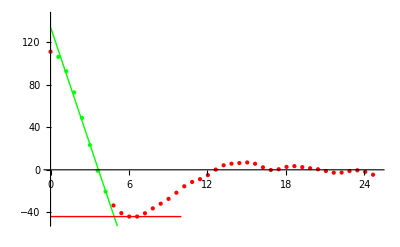

```mathematica
(*Import Data from files*)
Clear[lFit];
prefix = "PET-";
sample = "215";
path = ParentDirectory[NotebookDirectory[]] <> "/data/" <> prefix <> sample;
rawData=Import[path<>".cor","Table"];


(*Split Data into parts for linear fit and for the rest*)
sampleSize = 9;
linearData =  Take[rawData, {2,sampleSize}];
afterLinearData =  Take[rawData, -(Length[rawData ] - sampleSize)];
nonLinearData = Join[Take[rawData, 1], afterLinearData];

(*Find Min and Max of data, also find 2nd local max*)
minMax = {First@SortBy[rawData,Last], Last@SortBy[rawData,Last]};
localMax = Last@SortBy[afterLinearData,Last];

(*Linear fit*)
lFit = LinearModelFit[linearData,x,x];


(*Relevant points*)
q = lFit["Function"][0]
dc = Solve[lFit["BestFit"] == minMax[[1]][[2]], x][[All, 1, 2]][[1]]
dac = localMax[[1]]
dacy = localMax[[2]]


Export[path<>"-Q-Dc-Dac-Dacy.cor", {q, dc, dac, dacy}, "Table"];
Export[path <> ".cor.fit", lFit["BestFit"], "String"];

(*Plot functions and data*)
Show[ListPlot[nonLinearData,PlotStyle->Red], ListPlot[linearData,PlotStyle->Green], Plot[{lFit["BestFit"]},{x,0,8}, PlotStyle-> Green],Plot[{minMax[[1]][[2]]},{x,0,10}, PlotStyle-> Red], PlotRange-> {{0,25},{minMax[[1]][[2]] - 5,lFit["Function"][0]+ 10}}]
```